```mathematica
SetOptions[{Plot, ListPlot,LogLogPlot,LogLinearPlot,LogPlot,ListLogLinearPlot},GridLines->Automatic];
```

π[x] – number of primes numbers ≤ x, aka prime counting function.

### Prime numbers

```mathematica
Prime[ Range[30]]
```

```mathematica
Accumulate[{a,b,c,d}]
```

```mathematica
Accumulate[Prime[ Range[30]]]
```

```mathematica
primes1K=Prime[ Range[1000]];
```

```mathematica
{primes1K, Accumulate[primes1K^1]}ᵀ
```

```mathematica
ListPlot[{primes1K, Accumulate[primes1K^1]}ᵀ]
```

```mathematica
ListPlot[{primes1K, Log[primes1K^1]Accumulate[primes1K^1]}ᵀ]
```

```mathematica
ListPlot[{primes1K, Accumulate[primes1K^-1]}ᵀ]
```

```mathematica
{primes1K, Accumulate[primes1K^0]}ᵀ
```

```mathematica
ListPlot[{primes1K, Accumulate[primes1K^0]}ᵀ]
```

```mathematica
Accumulate[primes1K^0]==Range[Length[primes1K]]
```

### Let’s crack primes counting π function

Number of prime numbers ≤ x

```mathematica
primes30=Prime[Range[30]];
```

```mathematica
gl=ListPlot[{primes30, Accumulate[primes30^0]}ᵀ,PlotStyle->Orange,Joined->True]
```

```mathematica
primes=N[Prime[ Range[3002195]]];
primePi = Accumulate[primes^0];
```

But we have already PrimePi function in Mathematica

```mathematica
PrimePi[2] (* {2} *)
```

```mathematica
PrimePi[10] (* {2,3,5,7} *)
```

```mathematica
PrimePi[600000000000]
```

```mathematica
g=Plot[PrimePi[x],{x,0,70},PlotPoints->200]
```

```mathematica
Show[g,gl]
```

```mathematica
Plot[PrimePi[x]/x,{x,2,1000000},PlotRange->{Automatic,{0,Automatic}}]
```

8 % of numbers are prime in [1, 1 000 000]

```mathematica
f[x_]:= PrimePi[x]/x;
Plot[f[Exp[lx]],{lx,2,30}]
```

```mathematica
f[x_]:= PrimePi[x]/(x /Log[x]);
Plot[f[Exp[lx]],{lx,2,30}]
```

Theorem: lim_(x→ ∞) PrimePi[x]/(x /Log[x]) = 1

```mathematica
f[x_,a_]:= PrimePi[x]-x/Log[x]^a; (* <- wrong idea *)
```

```mathematica
f[x_,a_]:= PrimePi[x]-x/(Log[x]-a);
Manipulate[
Plot[f[x,a],{x,2,50000000}],
{{a,1.086},0.5,1.5}
]
```

```mathematica
f[x_,a_]:= (PrimePi[x]-x/(Log[x]-a));
Manipulate[
Plot[{f[x,a],0.01b x^c },{x,2,10000000},PlotPoints->50],
{{a,1.05},0.9,1.2},
{{b,2.1},0.001,4},
{{c,0.67},0.1,0.8}
]
```

```mathematica
f[x_,a_,b_,c_]:= (PrimePi[x]-x/(Log[x]-a)-0.01b x^c )/Sqrt[x];
Manipulate[
Plot[f[x,a,b,c],{x,2,10000000},PlotPoints->50],
{{a,1.05},0.9,1.2},
{{b,2.1},0.001,4},
{{c,0.67},0.1,0.8}
]
```

```mathematica
f[x_,a_,b_,c_]:= (PrimePi[x]-x/(Log[x]-a)-0.01b x^c +40)/Sqrt[x];
Manipulate[
Plot[f[x,a,b,c],{x,2,10000000},PlotPoints->50,  AspectRatio->1/4],
{{a,1.05},0.9,1.2},
{{b,2.1},0.001,4},
{{c,0.67},0.1,0.8}
]
```

```mathematica
(π-x/(Log[x]-1.05)-0.021 x^0.67+40)/Sqrt[x]==noise
```

```mathematica
Solve[
(pi-n / (Log[n]-1.05)-0.021 n^0.67 + 40) / Sqrt[n]==noise,
pi
]//Expand
```

This is bad approximation. It' s just for illustration

### Define big sums for primes and powers of primes

```mathematica
primesPowersUpTo50=Transpose[
{#,FactorInteger[#][[1,1]]}&/@(Select[#,PrimePowerQ[#]&]&[Range[50]])
]
```

```mathematica
{pp,p}=primesPowersUpTo50;
Log[p]pp
```

```mathematica
primesPowersUpTo1K=Transpose[
{#,FactorInteger[#][[1,1]]}&/@(Select[#,PrimePowerQ[#]&]&[Range[1000]])
];
{pp,p}=primesPowersUpTo1K;
```

```mathematica
t=Accumulate[Log[p]pp];
```

```mathematica
ListPlot[{{pp,t}ᵀ}]
```

```mathematica
ListPlot[{{pp,Sqrt[pp](t/pp^2-0.5)}ᵀ}]
```

```mathematica
ListPlot[{{pp,Sqrt[pp](t/pp^2-0.5)}ᵀ}]
```

```mathematica
t=Accumulate[Log[p]/pp];
```

```mathematica
ListPlot[{{pp,t}ᵀ,{pp,Log[pp]}ᵀ}] (* Log like? *)
```

```mathematica
ListPlot[{pp,t-Log[pp]}ᵀ]
```

```mathematica
ListPlot[{pp,Sqrt[pp](t-Log[pp]+0.57)}ᵀ]
```

```mathematica
primesPowersUpTo50M = N[Transpose[
{#,FactorInteger[#][[1,1]]}&/@(Select[#,PrimePowerQ[#]&]&[Range[50000000]])
]];
```

```mathematica
primes=N[Prime[ Range[3002195]]];
```

```mathematica
sumPLog={primes,Accumulate[Log[primes]]}ᵀ;
sumPp1={primes,Accumulate[primes]}ᵀ;
sumPp2={primes,Accumulate[primes^2]}ᵀ;
sumPp3={primes,Accumulate[primes^3]}ᵀ;
sumPp4={primes,Accumulate[primes^4]}ᵀ;
sumPp0={primes,Accumulate[primes^0]}ᵀ; (* PrimePi function *)
sumPr1={primes,Accumulate[1/primes]}ᵀ;
sumPp1Log={primes,Accumulate[primes Log[primes]]}ᵀ;
sumPr1Log={primes,Accumulate[ Log[primes]/primes]}ᵀ;
sumPp2Log={primes,Accumulate[primes^2 Log[primes]]}ᵀ;
sumPp3Log={primes,Accumulate[primes^3 Log[primes]]}ᵀ;
sumPp4Log={primes,Accumulate[primes^4 Log[primes]]}ᵀ;
```

```mathematica
SumPn[s_]:=SumPn[s]={primes,Accumulate[ 1/primes^s]}ᵀ;
SumPnLog[s_]:=SumPnLog[s]={primes,Accumulate[ Log[primes]/primes^s]}ᵀ;
SumPmLog[s_]:=SumPmLog[s]={primes,Accumulate[ Log[primes](1/(primes^s-1))]}ᵀ;
```

```mathematica
sumPm1Log=SumPmLog[1];
sumPm2Log=SumPmLog[2];
```

```mathematica
{pp,p}= primesPowersUpTo50M ;
sumPPLog={pp,Accumulate[Log[p]]}ᵀ;
sumPPp1={pp,Accumulate[pp]}ᵀ;
sumPPp3Log={pp,Accumulate[pp^3 Log[p]]}ᵀ;
sumPPp4Log={pp,Accumulate[pp^4 Log[p]]}ᵀ;
sumPPr1={pp,Accumulate[1/pp]}ᵀ;
sumPPp1Log={pp,Accumulate[pp Log[p]]}ᵀ;
sumPPp2Log={pp,Accumulate[pp^2 Log[p]]}ᵀ;
sumPPr1Log={pp,Accumulate[Log[p]/pp]}ᵀ;
```

```mathematica
SumPPn[s_]:=SumPPn[s]={pp,Accumulate[ 1/pp^s]}ᵀ;
SumPPnLog[s_]:=SumPPnLog[s]={pp,Accumulate[ Log[p]/pp^s]}ᵀ;
```

```mathematica
{pp,p}= primesPowersUpTo50M ;
sumPPPLog={pp,Accumulate[Log[p]]}ᵀ;
sumPPPp1={pp,Accumulate[p]}ᵀ;
sumPPPr1={pp,Accumulate[1/p]}ᵀ;
sumPPPp1Log={pp,Accumulate[p Log[p]]}ᵀ;
sumPPPr1Log={pp,Accumulate[Log[p]/p]}ᵀ;
sumPPPp2Log={pp,Accumulate[p^2 Log[p]]}ᵀ;
```

```mathematica
SumPPPn[s_]:=SumPPPn[s]={pp,Accumulate[ 1/p^s]}ᵀ;
SumPPPnLog[s_]:=SumPPPnLog[s]={pp,Accumulate[ Log[p]/p^s]}ᵀ;
```

P stands for Primes.
PP stands for Primes Powers.
f(pp, p) = pp^-s Log[p]

P sum ==  ∑_(p ∈ Primes) f(p,p)

PP sum ==  ∑_(pp ∈  Primes Powers
pp = p^k) f(pp, p)
PPP sum ==  ∑_(pp ∈  Primes Powers
pp = p^k) f(p, p)

### Rationale

ζ[s_]:=∑_(n=1)^∞ 1/n^s
ζ[2]== 1/1^2+1/2^2+1/3^2+ ...; (* Basel Problem, solved by Euler in 1734 *)

1/ζ[k] == Probability that k random intergers are coprime.

ζ[s]==∑_(n=1)^∞ 1/n^s=∏_(p ∈ Primes)^∞ (1+1/p^s+1/p^(2s)+1/p^(3s)+...)=1/(∏_(p ∈ Primes)^∞ (1-1/p^s));

Zeros and poles are the subject of investigation.

∂_s log(f(s)) reveals some properties.

∂_s log(f(s))  gives k/(s-s_0) for zeros and poles:
 f(s)== (s-s_0)^k (a_0+a_1 s +a_2 s + ...)
	log(f(s)) == k log(s-s_0) + log(a_0+a_1 s +a_2 s^2 +...)
	∂_s log(f(s)) == k/(s-s_0) + (a_1 +2 a_2 s +...)/(a_0+a_1 s +a_2 s +...)

∏_(p ∈ Primes)^∞ (1-1/p^s)==∑_(n=1)^∞ (μ(n))/n^s, where  μ(n) is Möbius function == 1,-1 or 0

∂_s (∑_(n=1)^∞ (μ(n))/n^s)==-∑_(n=1)^∞ μ(n) (log(n))/n^s
∂_s log(∏_(p ∈ Primes)^∞ (1-1/p^s))==-∑_(p ∈ Primes) (1 log(p)1/p^s)/(1-1/p^s)
=-∑_(p ∈ Primes) log(p)(1/p^s+1/p^(2s)+1/p^(3s)+...)

### Sums over primes and powers of primes ∑ Log[p]

ξ[n_]:=∑_(p ∈ Primes,
p ≤ n) Log[p];

Pξ[n_]:=∑_(p^k ∈ PrimePowers,
p^k ≤ n) Log[p];

Pξ[n_]:=∑_(p ∈ Primes,) Log[p] Floor[Log[n]/Log[p]];

ξ[5^3]== ... + Log[5] + ...
Pξ[5^3]== ... + 3 Log[5] + ...

ξ[n]+ξ[n^(1/2)]+ξ[n^(1/3)]+ξ[n^(1/4)]+...==  Pξ[n];
n = 5^3
Log[5] + Log[5] + Log[5] + 0 + 0 +... = 3 Log[5]

```mathematica
n = 5^12
Pξ[n] - Pξ[n^(1/2)]- Pξ[n^(1/3)] - Pξ[n^(1/5)]+Pξ[n^(1/6)]- Pξ[n^(1/7)]+ Pξ[n^(1/10)]- Pξ[n^(1/11)]+...==ξ[n]
12         - 6             - 4               - 2               + 2              - 1              +  1               -1  ==  1
```

Numbers
1, 2, ..., n
Lets remove from this set all numbers except for 1. Lets remove:
  - numbers divided by 2 (= |n/2|,   Lets denote Floor[x] as |x|)
  - numbers divided by 3 (= |n/3|)
  - numbers divided by 5 (= |n/5|)
  - numbers divided by 7 (= |n/7|)
  - .. 
 But we remove number 6=2 * 3 two times;
 So lets add  |n/6|. We get 
 n - |n/2| - |n/3| - |n/5| - |n/7| - ...  + |n/6| + |n/10| + |n/14| + ...
 But now number i = 2 * 3 * 5 still presents: 1 - 3 + 3. Need to subtract |n/30 |
 n - |n/2| - |n/3| - |n/5| - |n/7| - ...  + |n/6| + |n/10| + |n/14| + ...  - |n/(2*3*5)| - |n/(2*3*7)|+
 So
 (∑^m)_(k=1) μ[k]Pξ[n^(1/k)]== ξ[n]

```mathematica
n=133;
Plus@@Table[ Floor[n/k] MoebiusMu[k],{k,1,n}]
```

### Sums over primes and powers of primes ∑ k^m Log[p]

```mathematica
ψ[n_]:=∑_(p ∈ Primes,
p ≤ n) Log[p];

Pψ[n_]:=∑_(p^k ∈ PrimePowers,
p^k ≤ n) k^2 Log[p];
Pψ[n_]:=∑_(p ∈ Primes) (1+2 + ... +Floor[Log[n]/Log[p]])Log[p];
```

```mathematica
ψ[5^4]=...+Log[5]+...
Pψ[5^4]=...+(1 + 2 + 3 + 4)Log[5]+...
```

```mathematica
ψ[n]+2ψ[n^(1/2)]+3ψ[n^(1/3)]+4ψ[n^(1/4)]+...== Pψ[n]
1       + 2             + 3              + 4     + 0 + 0 ... = 10
```

```mathematica
n=12;
Plus@@Table[ k 1/2 Floor[n/k] (Floor[n/k]+1)MoebiusMu[k],{k,1,n}]
```

```mathematica
Pψ[n] -2 Pψ[n^(1/2)]-3Pψ[n^(1/3)]- 5Pψ[n^(1/5)]+ 6Pψ[n^(1/6)]- 7Pψ[n^(1/7)]+ 10Pψ[n^(1/10)]..=ψ[n]
```

```mathematica
f[n_]:=n;
expr=(
1+2 + 3 + 4+5+6+7+8+9+10+11+ 12
-f[2](1+2 +3+4+5 + 6)
-f[3](1+2+  3 + 4)
-f[5](1+2)
+f[6](1+2)
-f[7](1)
+f[10](1)
-f[11](1)
)//Expand
```

```mathematica
n=12;
l=Table[Plus@@Table[ k 1/2 Floor[n/k] (Floor[n/k]+1)MoebiusMu[k],{k,1,n}],{n,40}]
```

```mathematica
Sum[k^2,{k,1,m}]
```

```mathematica
Sum[k^3,{k,1,m}]
```

```mathematica
g[m_,2]:=1/6 m (1+m) (1+2 m);
g[m_,3]:=1/4 m^2 (1+m)^2;
```

```mathematica
l=Table[Plus@@Table[ k^2 g[Floor[n/k],2]MoebiusMu[k],{k,1,n}],{n,40}]
```

```mathematica
l=Table[Plus@@Table[ k^3 g[Floor[n/k],3]MoebiusMu[k],{k,1,n}],{n,40}]
```

```mathematica
HarmonicNumber[1]
```

```mathematica
l=Table[Plus@@Table[ 1/k HarmonicNumber[Floor[n/k]]MoebiusMu[k],{k,1,n}],{n,40}]//N
```

See -Graphics- and reverse formula in https://en.wikipedia.org/wiki/Chebyshev_function#Relation_to_the_prime-counting_function

```mathematica
l=Table[Plus@@Table[ 1/k^2 HarmonicNumber[Floor[n/k],2]MoebiusMu[k],{k,1,n}],{n,40}]//N
```

```mathematica
ListPlot[l]
```

### Sums MoebiusMu

```mathematica
ListPlot[Accumulate[MoebiusMu[Range[1000]]],AspectRatio->1/3]
```

```mathematica
n=1000000;
ListPlot[{
ListQPart[{Log[Range[n]], 1/Sqrt[Range[n]] Accumulate[MoebiusMu[Range[n]]]}ᵀ,10000]
},AspectRatio->1/3]
```

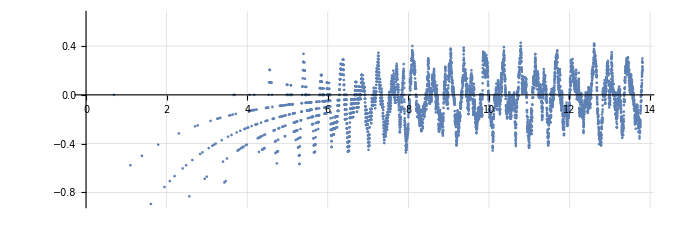

### Sums ∑ 1/p^s Log[p]

```mathematica
ψ[n_]:=∑_(p ∈ Primes,
p ≤ n) Log[p]/p^s;

Pψ[n_]:=∑_(p^k ∈ PrimePowers,
p^k ≤ n) 1/p^ks Log[p];
Pψ[n_]:=∑_(p ∈ Primes) (1-(1/p^s)^Floor[Log[n]/Log[p]])/(p^s-1)Log[p];
```

```mathematica
expr=(
1/1+1/p+1/p^2+1/p^3+1/p^4+ 1/p^5+1/p^6+1/p^7+ 1/p^8+1/p^9+1/p^10+1/p^11+ 1/p^12
-1(1/1+1/p+1/p^2+1/p^3+1/p^4+1/p^5+1/p^6)
-1(1/1+1/p+1/p^2+1/p^3+1/p^4)
-1(1/1+1/p)
+1(1/1+1/p)
-1(1/1)
+1(1/1)
-1(1/1)
)//Expand
```

```mathematica
pp=3;
Plus@@Table[ Floor[Log[pp,n]] MoebiusMu[n],{n,1,120}]
```

```mathematica
pp=5;
Series[Plus@@Table[(1-1/(z pp)^Floor[Log[pp,n]])/((z pp)-1)MoebiusMu[n],{n,1,12}],{z,∞,9}]
```

```mathematica
Pψ[n] -1/2 Pψ[n^(1/2)]- 1/3 Pψ[n^(1/3)]- 1/5 Pψ[n^(1/5)]+ 1/6 Pψ[n^(1/6)]- 1/7 Pψ[n^(1/7)]+ 1/10 Pψ[n^(1/10)];

expr=(
1/1+1/p+1/p^2+1/p^3+1/p^4+ 1/p^5+1/p^6+1/p^7+ 1/p^8+1/p^9+1/p^10+1/p^11+ 1/p^12
-1/2(1/1+1/p+1/p^2+1/p^3+1/p^4+1/p^5+1/p^6)
-1/3(1/1+1/p+1/p^2+1/p^3+1/p^4)
-1/5(1/1+1/p)
+1/6(1/1+1/p)
-1/7(1/1)
+1/10(1/1)
-1/11(1/1)
)//Expand
```

```mathematica
expr/.{p->5}
```

```mathematica
muR1=({Range[#],Table[MoebiusMu[n]/n,{n,#}]}ᵀ)&[100000]//Accumulate//N;
ListPlot[{Log[#⟦1⟧],Log[#⟦1⟧]^2#⟦2⟧}&/@muR1,AspectRatio->1/4]
```

### Library

```mathematica
QRange[k_,nSteps_,prefix_]:=DeleteDuplicates[Sort[Join[Range[prefix], Round[Exp[# Log[k]/nSteps]&/@Range[nSteps]]]]
] ;
QRange[k_,nSteps_]:=QRange[k,nSteps,100] ;
```

```mathematica
QRange[1000,100,5]
```

```mathematica
ListQPart[l_,nSteps_,prefix_]:=l⟦QRange[Length[l],nSteps,prefix]⟧;
ListQPart[l_,nSteps_]:=ListQPart[l,nSteps,100];
```

```mathematica
CatXYs[l1_,l2_]:={#⟦1,1⟧,#⟦1,2⟧,#⟦2,2⟧}&/@({l1,l2}ᵀ);
CatXYs[ls_]:=(Flatten[{Sequence[#⟦1,1⟧], (#⟦2⟧&/@#)}])&/@(lsᵀ)
```

### P sum of 1, aka π(n) function – approximating by log(n) and n^k

```mathematica
dataPi=ListQPart[sumPp0,10000];
ListPlot[{#⟦1⟧,#⟦2⟧}&/@dataPi]
```

```mathematica
ListPlot[{Log[#⟦1⟧],#⟦2⟧/#⟦1⟧}&/@dataPi]
```

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-(#⟦1⟧)/(Log[#⟦1⟧]-1.05)}&/@dataPi]
```

```mathematica
1.065
```

```mathematica
Manipulate[
ListPlot[
{
{#⟦1⟧,#⟦2⟧-(#⟦1⟧)/(Log[#⟦1⟧]-a 1.065)}&/@dataPi,
{#⟦1⟧, 0.001c (#⟦1⟧)^(b 0.7)Log[#⟦1⟧]}&/@dataPi
},PlotRange->{Automatic,{0,maxy}}
],
{{a,0.995},0.5,1.5},
{{b,0.798},0.25,2},
{{c,4.37},0.1,10},
{{maxy,1000},1,20000}
]
```

```mathematica
Manipulate[
ListPlot[
{
{
Log[#⟦1⟧],
Log[#⟦1⟧](
(
#⟦2⟧-(#⟦1⟧)/(Log[#⟦1⟧]-a 1.065)-0.01c (#⟦1⟧)^(b 0.7)(Log[#⟦1⟧]-a2 1.065)
 )/Sqrt[#⟦1⟧] + d
)
}&/@dataPi
},PlotRange->{Automatic,{-maxy,maxy}},AspectRatio->1/3,ImageSize->Large
],
{{a,0.987},0.6,1.2},
{{a2,0},-2,2},
{{b,0.805},0.5,1.2},
{{c,1},0.1,10},
{{d,0.15},-0.5,0.5},
{{maxy,5},1,20}
]
```

```mathematica
rules={a->0.987,a2->0,b->0.805,c->1,d->0.15};
```

```mathematica
Solve[
Log[n]((pi-n/(Log[n]-a 1.065)-0.01c n^(b 0.7)(Log[n]-a2 1.065) )/Sqrt[n] + d)==noise/.rules,
pi
]//Expand
```

```mathematica
PrimePiApprox[n_]:=n/(-1.051+Log[n]);
```

```mathematica
PrimePi[50000000000]
```

```mathematica
n=50000000000000;
PrimePi[n]/PrimePiApprox[n]
```

```mathematica
Clear[n];
Solve[
n/(-1.0a+Log[n])==PrimePi[n]/.{n->500000000000},
a
]
```

```mathematica
{{pi->-0.15 √n+(1. n)/(-1.051155+Log[n])+(1. √n noise)/Log[n]+0.01 n^0.5635 Log[n]}}
```

### Find coeffs for π approx by minimizing noise ATTEMPT0

```mathematica
expr=n/(-a+Log[n])+c n^d +e+√n (noise-b);
```

```mathematica
Clear[n];
Solve[pi==expr,noise]//FullSimplify
```

```mathematica
Noise[n_]:=(e-b √n+c n^d-PrimePi[n]+n/(-a+Log[n]))/(√n);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(10+QRange[500000000000,2000,5]));
solution=NMinimize[
loss,
{{a,0.9,1.2},{b,-0.5,0.5},{c,0.0002, 0.1},{d,0.2,0.76},{e,-4,4}},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#] }&/@(2+QRange[5000000000000,5000,100])]
```

### Find coeffs for π approx by minimizing noise ATTEMPT1

```mathematica
expr=n/(-a+Log[n])+c n^d +e+√n (noise-b);
```

```mathematica
expr=n/(-a+Log[n])+c n^d+e+(√n (noise-b))/Log[n];
```

```mathematica
Clear[n];
Solve[pi==expr,noise]//FullSimplify
```

```mathematica
Noise[n_]:=(Log[n] (e+c n^d-PrimePi[n]-(b √n)/Log[n]+n/(-a+Log[n])))/(√n);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(10+QRange[500000000000,2000,5]));
solution=NMinimize[
loss,
{{a,0.9,1.2},{b,-0.5,0.5},{c,0.0002, 0.1},{d,0.2,0.76},{e,-4,4}},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#] }&/@(2+QRange[5000000000000,5000,100])]
```

### Find coeffs for π approx by minimizing noise ATTEMPT2

```mathematica
expr=n/(-a+Log[n])+(b3 n)/(Log[n])^3+(b4 n)/(Log[n])^4+(b5 n)/(Log[n])^5+(√n (noise+d))/Log[n]+e;
```

```mathematica
Clear[n];
Solve[pi==expr,noise]
```

```mathematica
Noise[n_]:=(Log[n] (e-PrimePi[n]+(b5 n)/Log[n]^5+(b4 n)/Log[n]^4+(b3 n)/Log[n]^3+(d √n)/Log[n]+n/(-a+Log[n])))/(√n);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(2+QRange[500000000000,2000,5]));
solution=NMinimize[
loss,
{{a,0.95,1.1},{b3,-1,1},{b4,-10,10},{b5,-10,10},{d,-1.5,1.5},{e,-3,3}},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#]}&/@(2+QRange[500000000000,5000,100]),AspectRatio->1/4,AxesLabel->{"Log[x]","noise"},AxesOrigin->{0,-0.5}]
```

```mathematica
ListPlot[{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#]}&/@(2+QRange[500000000000,5000,100]),AspectRatio->1/4,AxesOrigin->{0,-0.5}]
```

```mathematica
Series[1/(-1.005182+Log[n])-28.7385/Log[n]^5+13.1891/Log[n]^4+0.62466/Log[n]^3,{Log[n],∞,6}]//Expand
```

### Find coeffs for π approx by minimizing noise ATTEMPT3

```mathematica
expr=n/(-a+Log[n])+(b3 n)/(Log[n])^3+(b4 n)/(Log[n])^4+(b5 n)/(Log[n])^5+(√n (noise+d))/Log[n]+e;
```

```mathematica
expr=n/Log[n](1+b1/(Log[n])^1+b2/(Log[n])^2+b3/(Log[n])^3+b4/(Log[n])^4)+(√n (noise+d))/Log[n]+e;
```

```mathematica
Clear[n];
Solve[pi==expr,noise]
```

```mathematica
Noise[n_]:=d+Log[n]/(√n) (
e-PrimePi[n]+n/Log[n] (1+b4/(Log[n])^4+b3/(Log[n])^3+b2/(Log[n])^2+b1/Log[n])
);
```

```mathematica
loss=Mean@(Noise[#]^2&/@(2+QRange[500000000000,4000,5]));
solution=NMinimize[
loss,
{b1,b2,b3,b4,d,e},
Method->"SimulatedAnnealing"
]
```

```mathematica
PrimePiMy[n_]:=Evaluate[expr/.solution[[2]]/.{noise->0}];
PrimePiMy[n]
```

```mathematica
ListPlot[
{Log[#],(PrimePiMy[#]- PrimePi[#])/Sqrt[#] Log[#]}&/@(2+QRange[5000000000000,5000,100]),
AspectRatio->1/4,ImageSize->Large
]
```

### P sum of 1, aka π(n) function – approximating by Li(n)

```mathematica
∫_2^y 1/Log[x] ⅆx
```

```mathematica
∫_0^y (1/Log[x]-1/(x-1))ⅆx
```

```mathematica
Assuming[{x>0},Series[LogIntegral[x],{x,∞,5}]]//Normal//Expand
```

```mathematica
Assuming[{x>0},Series[LogIntegral[x]/x,{x,∞,5}]]//Normal//Expand
```

```mathematica
Assuming[{x>0},Series[LogIntegral[Exp[x]]/Exp[x],{x,∞,16}]]//Normal//Expand
```

```mathematica
PrimePiMy[x]
```

```mathematica
Nn[x_]:=Sqrt[x]/Log[x];
f0[x_]:= 1/Nn[x](PrimePi[x]-x/(Log[x]-1.05));
f[x_]:= 1/Nn[x](PrimePi[x]-PrimePiMy[x]);
h[x_]:=1/Nn[x](PrimePi[x]-LogIntegral[x]+1/2LogIntegral[Sqrt[x]]);
LogLinearPlot[
{f0[x],f[x], h[x]},
{x,2,500000000},PlotPoints->50,  AspectRatio->1/3,ImageSize->Large
]
```

### Riemann formula for π (n) approx based on Li (n)

```mathematica
R[x_,n_]:=∑_(i=1)^n MoebiusMu[i]/i LogIntegral[Exp[Log[x]/i]];
```

```mathematica
R[x,17]
```

```mathematica
PrimePiLIApprox[x_,n_]:=R[x,n] + 1/π ArcTan[π/Log[x]]-1/Log[x]
```

```mathematica
LogLogPlot[-1/π ArcTan[π/x]+1/x,{x,2,10000},PlotRange->{Automatic,{0,Automatic}}]
```

```mathematica
Nn[x_]:=Log[x]/Sqrt[x];
LogLinearPlot[{
Nn[x](PrimePi[x]-x/(Log[x]-1.05)),
Nn[x](PrimePi[x]-PrimePiMy[x]),
Nn[x](PrimePi[x]-LogIntegral[x]+1/2 LogIntegral[Sqrt[x]]),
Nn[x] (PrimePi[x]-PrimePiLIApprox[x,3])
},{x,1,1000000000}]
```

```mathematica
PrimePiMy[x]
```

```mathematica
Nn[x_]:=Log[x]/Sqrt[x];
LogLinearPlot[{
Nn[x](PrimePiMy[x]-PrimePiLIApprox[x,150])
},{x,1,10000000000000},PlotRange->{Automatic,{-0.5,0.5}}
]
```

### TAKEAWAYS for π

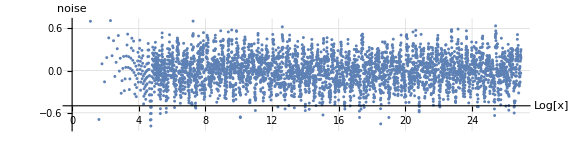
Take aways
1)  π[x] ~x/Log[x],  and    lim_(x→ ∞)  π[x] /x/Log[x]=1  
2) It is easy to get The Noise exploring PrimePi function :  π[x]-x/Log[x]-(b_1 x)/Log[x]^2-(b_2 x)/Log[x]^3-...
We came to
π[x] =x/Log[x](1+b_1/Log[x]+b_2/Log[x]^2+b_3/Log[x]^3+...)+(√x)/Log[x]noise_1[x]
where noise_1[x] is (as function of Log[x])
-Graphics-
3) NMinimize could be uses to fit coefficients {b_1,b_2,...} of approx formulas. 
And simple check for extrapolation shows correctness of the formula.
4) Good PrimePi approximation (Riemann) is based on LogIntegral function. 
li[x]=∫_0^x 1/Log[t]ⅆt
How can one come to the idea of estimating |π[x] - li[x]|? It is poorly covered on the Internet.

It looks like

π[x]= li[x]+(√x)/Log[x]noise
but more precise fact (not proven here) is

π[x]= R[x]+ η[x] +(√x)/Log[x]noise,
where
    R[x]= li[x]-1/2 li[x^(1/2)]-1/3 li[x^(1/3)]-1/5 li[x^(1/5)]+1/6 li[x^(1/6)]+..;
    η[x]= 1/π arctan(π/Log[x])-1/Log[x]=O[1/Log[x]^2].

5)  (√x)/Log[x]noise<C √x Log[x] is equivalent to Riemann hypothesis.

noise<C Log[x]^2

Riemann hypothesis == non trivial zeros of ζ-function lay on line Re[z]==1/2.
ζ[z] := analytic continuation of ζ[z]=∑_(k=1)^∞ 1/k^z.

### FULL Riemann formula for π (n) based on Li (n)

```mathematica
R[x_,n_]:=∑_(i=1)^n MoebiusMu[i]/i LogIntegral[x^(1/i)];
```

```mathematica
R2[x_,mul_,n_]:=∑_(i=1)^n MoebiusMu[i]/i Re[-ExpIntegralE[1,-mul Log[x]/i]];
```

```mathematica
{R[2.2,13],R2[2.2,1,13]}
```

```mathematica
PrimePiLIApprox[x_,n_]:=R[x,n] + 1/π ArcTan[π/Log[x]]-1/Log[x]+1/2;
```

```mathematica
gNoise=ListLogLinearPlot[
(Log[#]/Sqrt[#](PrimePi[#]-PrimePiLIApprox[#,150]))&/@N[Prime[Range[1,6000]]],
PlotStyle->{PointSize[0.009], RGBColor[0.87,0.3,0.25]}
]
```

```mathematica
ZetaZero[Range[10]]//N
```

```mathematica
zeros=ZetaZero[Range[100]]//N;
```

```mathematica
{R2[2.2,zeros⟦3⟧,13],R2[2.2,Conjugate[zeros⟦3⟧],13]}
```

```mathematica
RiemannNoise[x_,n_,m_]:=-2∑_(k=1)^m R2[x,zeros⟦k⟧,n]
```

```mathematica
LogLinearPlot[Re[RiemannNoise[x,60,1]],{x,2,1000}]
```

```mathematica
Manipulate[
Show[
LogLinearPlot[Log[x]/Sqrt[x] Re[RiemannNoise[x,n,m]],{x,2,100}],
gNoise
],
{{n,10},1,15,1},
{{m,10},1,15,1}
]
```

### P sum of log(p)

```mathematica
data=ListQPart[sumPLog,1000];
ListPlot[{#⟦1⟧,#⟦2⟧-#⟦1⟧}&/@data]
```

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-#⟦1⟧+Sqrt[#⟦1⟧]}&/@data]
```

```mathematica
data=ListQPart[sumPLog,10000];
ListPlot[
{Log[#⟦1⟧],(#⟦2⟧-#⟦1⟧+Sqrt[#⟦1⟧])/Sqrt[#⟦1⟧]}&/@data, 
AspectRatio->1/5
]
```

### PP sum of log(p)

Chebyshev function
https://en.wikipedia.org/wiki/Chebyshev_function

```mathematica
data=ListQPart[sumPPLog,10000];
ListPlot[{#⟦1⟧,#⟦2⟧}&/@data,AspectRatio->1/5]
```

```mathematica
ListPlot[{Log[#⟦1⟧],(#⟦2⟧-#⟦1⟧)/Sqrt[#⟦1⟧]}&/@data,AspectRatio->1/5]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],(#⟦2⟧-#⟦1⟧+1.84)/Sqrt[#⟦1⟧]}&/@data
},
AspectRatio->1/5
]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],(#⟦2⟧-#⟦1⟧+1.84-(1/2)/(#⟦1⟧)^2)/Sqrt[#⟦1⟧]}&/@data
},
AspectRatio->1/5
]
```

∑_(p^k≤ n) Log[p]=n -Log[2 π]+1/(2 n^2)+√n noise

```mathematica
Log[2 Pi]//N
```

### P sum of 1/p

https://en.wikipedia.org/wiki/Mertens%27_theorems

```mathematica
data=ListQPart[sumPr1,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧}&/@data,
{Log[#⟦1⟧],Log[Log[#⟦1⟧]]}&/@data
}
]
```

See Meissel–Mertens constant
M ≈ 0.2614972128476427837554268386086958590516.

```mathematica
data=ListQPart[sumPr1,10000];
ListPlot[{
{Log[#⟦1⟧],(#⟦2⟧-Log[Log[#⟦1⟧]]-0.2614972)}&/@data
}
]
```

```mathematica
data=ListQPart[sumPr1,10000];
ListPlot[{
{Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[Log[#⟦1⟧]]-0.2614972)}&/@data
}
]
```

```mathematica
data=ListQPart[sumPr1,10000];
ListPlot[{
{Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[Log[#⟦1⟧]]-0.26149721)-0.057}&/@data,
{Log[#⟦1⟧],5/Sqrt[#⟦1⟧]}&/@data
}
]
```

```mathematica
data=ListQPart[sumPr1,10000];
ListPlot[{
{Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[Log[#⟦1⟧]]-0.26149721)-0.057-5/Sqrt[#⟦1⟧]}&/@data
}
]
```

### PP sum of 1/p

```mathematica
data=ListQPart[sumPPPr1,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧}&/@data,
{Log[#⟦1⟧],1.61Log[#⟦1⟧]-2}&/@data
}
]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧-1.61Log[#⟦1⟧]+2}&/@data,
{Log[#⟦1⟧],4/Sqrt[#⟦1⟧]}&/@data
}
]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧-1.61Log[#⟦1⟧]+2-4/Sqrt[#⟦1⟧]}&/@data,
{Log[#⟦1⟧],-8/#⟦1⟧}&/@data
}
]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧-1.61Log[#⟦1⟧]+2-4/Sqrt[#⟦1⟧]+8/#⟦1⟧}&/@data
}
]
```

### PP sum of 1/pp

```mathematica
data=ListQPart[sumPPr1,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧}&/@data,
{Log[#⟦1⟧],Log[Log[#⟦1⟧]]}&/@data
}
]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧-Log[Log[#⟦1⟧]]-1.0347}&/@data
}
]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[Log[#⟦1⟧]]-1.034655)+0.055}&/@data,
{Log[#⟦1⟧],-Log[#⟦1⟧]/Sqrt[#⟦1⟧]}&/@data
}
]
```

```mathematica
ListPlot[{
{
Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[Log[#⟦1⟧]]-1.034655)
+0.057
+Log[#⟦1⟧]/Sqrt[#⟦1⟧]
}&/@data
}
]
```

### P sum of p

```mathematica
data=ListQPart[sumPp1,10000];
ListPlot[{
{#⟦1⟧,#⟦2⟧}&/@data
}
]
```

```mathematica
data=ListQPart[sumPp1,10000];
ListPlot[{
{#⟦1⟧,#⟦2⟧}&/@data,
{#⟦1⟧,0.032(#⟦1⟧)^2}&/@data,
{#⟦1⟧,0.518(#⟦1⟧)^2/Log[#⟦1⟧]}&/@data,
{#⟦1⟧,0.518(#⟦1⟧)^2/(0.5 +Log[#⟦1⟧])}&/@data
}
]
```

```mathematica
EulerGamma//N
```

```mathematica
data=ListQPart[sumPp1,10000];
ListPlot[{
{#⟦1⟧,#⟦2⟧-0.4977(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216)}&/@data
}
]
```

```mathematica
data=ListQPart[sumPp1,10000];
ListPlot[{
{#⟦1⟧,(#⟦2⟧-0.49825(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/#⟦1⟧}&/@data,
{#⟦1⟧,-0.05Sqrt[#⟦1⟧]}&/@data
}
]
```

```mathematica
data=ListQPart[sumPp1,10000];
ListPlot[{
{
#⟦1⟧,
(#⟦2⟧-0.49825(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/#⟦1⟧
+0.05Sqrt[#⟦1⟧]
}&/@data
},AspectRatio->1/5
]
```

```mathematica
data=ListQPart[sumPp1,10000];
ListPlot[{
{
Log[#⟦1⟧],
(#⟦2⟧-0.49829(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/(#⟦1⟧)^1.5+0.06
}&/@data
},AspectRatio->1/5
]
```

### PP sum of p

```mathematica
data=ListQPart[sumPPPp1,10000];
ListPlot[{
{#⟦1⟧,#⟦2⟧}&/@data
}
]
```

```mathematica
ListPlot[{
{#⟦1⟧,#⟦2⟧}&/@data,
{#⟦1⟧,0.518(#⟦1⟧)^2/Log[#⟦1⟧]}&/@data
}
]
```

```mathematica
EulerGamma//N
```

```mathematica
ListPlot[{
{#⟦1⟧,#⟦2⟧-0.4977(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216)}&/@data
}
]
```

```mathematica
ListPlot[{
{#⟦1⟧,(#⟦2⟧-0.49825(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/#⟦1⟧}&/@data,
{#⟦1⟧,-0.05Sqrt[#⟦1⟧]}&/@data
}
]
```

```mathematica
ListPlot[{
{
#⟦1⟧,
(#⟦2⟧-0.49825(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/#⟦1⟧
+0.05Sqrt[#⟦1⟧]
}&/@data
},AspectRatio->1/5
]
```

```mathematica
data=ListQPart[sumPPPp1,10000];
ListPlot[{
{
Log[#⟦1⟧],
(#⟦2⟧-0.49829(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/(#⟦1⟧)^1.5+0.06
}&/@data
},AspectRatio->1/5
]
```

```mathematica
data=ListQPart[sumPp1,10000];
ListPlot[{
{
Log[#⟦1⟧],
(#⟦2⟧-0.49829(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/(#⟦1⟧)^1.5+0.06
}&/@data
},AspectRatio->1/5
]
```

### PP sum of pp

```mathematica
data=ListQPart[sumPPp1,10000];
ListPlot[{
{#⟦1⟧,#⟦2⟧}&/@data
}
]
```

```mathematica
ListPlot[{
{#⟦1⟧,#⟦2⟧}&/@data,
{#⟦1⟧,0.518(#⟦1⟧)^2/Log[#⟦1⟧]}&/@data
}
]
```

```mathematica
ListPlot[{
{#⟦1⟧,#⟦2⟧-0.498(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216)}&/@data
}
]
```

```mathematica
ListPlot[{
{#⟦1⟧,(#⟦2⟧-0.49825(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/(#⟦1⟧)^1.5}&/@data
}
]
```

```mathematica
data=ListQPart[sumPPp1,10000];
ListPlot[{
{
Log[#⟦1⟧],
(#⟦2⟧-0.49829(#⟦1⟧)^2/(Log[#⟦1⟧]-0.577216))/(#⟦1⟧)^1.5-4/(#⟦1⟧)^0.5+2/(#⟦1⟧)^1
}&/@data
},AspectRatio->1/5
]
```

### PP sum of Log[p]/pp

```mathematica
data=ListQPart[sumPPr1Log,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧}&/@data,
{Log[#⟦1⟧],Log[#⟦1⟧]}&/@data
}
]
```

```mathematica
data=ListQPart[sumPPr1Log,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧-Log[#⟦1⟧]}&/@data
}
]
```

```mathematica
data=ListQPart[sumPPr1Log,10000];
ListPlot[{
{Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[#⟦1⟧]+EulerGamma)}&/@data
},AspectRatio->1/5
]
```

### P sum of Log[p]/p

```mathematica
data=ListQPart[sumPr1Log,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧}&/@data,
{Log[#⟦1⟧],Log[#⟦1⟧]}&/@data
}
]
```

```mathematica
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧-Log[#⟦1⟧]}&/@data
}
]
```

Mertens' first theorem  ∑_(p ≤ n) Log[p]/p-Log[n] does not exceed 2 in absolute value for any n ≥ 2

```mathematica
data=ListQPart[sumPr1Log,10000];
ListPlot[{
{Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[#⟦1⟧]+1.3326)-1}&/@data
}, AspectRatio->1/4
]
```

### P sum of Log[p]/(p-1)

```mathematica
data=ListQPart[sumPm1Log,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧}&/@data,
{Log[#⟦1⟧],Log[#⟦1⟧]}&/@data
}
]
```

```mathematica
data=ListQPart[sumPm1Log,10000];
ListPlot[{
{Log[#⟦1⟧],#⟦2⟧-Log[#⟦1⟧]}&/@data
}
]
```

```mathematica
data=ListQPart[sumPm1Log,10000];
ListPlot[{
{Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[#⟦1⟧]+EulerGamma)-1}&/@data
}, AspectRatio->1/4
]
```

So

∑_(p≤ n) Log[p]/(p-1)=Log[n]-EulerGamma + 1/(√n)(noise+1)

Is it known result?

### P sum of Log[p]/(p^2-1)

```mathematica
dataPm2Log=ListQPart[sumPm2Log,10000];
```

```mathematica
ListPlot[{
{
Log[#⟦1⟧],
(#⟦2⟧- 0.569960993)
}&/@dataPm2Log
}
]
```

```mathematica
ListPlot[{
{
Log[#⟦1⟧],
(#⟦2⟧- 0.569960993)
}&/@dataPm2Log
}
]
```

```mathematica
ListPlot[{
{
Log[#⟦1⟧],
#⟦1⟧(#⟦2⟧- 0.569960993095)
}&/@dataPm2Log
}
]
```

```mathematica
Manipulate[
ListPlot[{
{
Log[#⟦1⟧],
#⟦1⟧(#⟦2⟧- 0.569960993095*(1+10^-10 a))+1
}&/@dataPm2Log,
{Log[#⟦1⟧],0.4/Sqrt[#⟦1⟧]}&/@dataPm2Log
}
],
{{a,-0},-1,1},
{{miny,1.0},0.1,15},
{{maxy,0.3},0.1,15}
]
```

```mathematica
Manipulate[
ListPlot[{
{
Log[#⟦1⟧],
Sqrt[#⟦1⟧](#⟦1⟧(#⟦2⟧- 0.569960993095*(1+10^-10 a))+1)-0.4 b
}&/@dataPm2Log
}
],
{{a,-0},-1,1},
{{b,1},0.1,3},
{{miny,1.0},0.1,15},
{{maxy,0.3},0.1,15}
]
```

```mathematica
Solve[Sqrt[x](x(sum- 0.569960993095)+1)-0.4 ==noise,sum]
```

∑_(p≤ n) Log[p]/(p^2-1)=0.569960993095-1/n+ 1/n^(3/2)(noise+0.4)
Is it known results?

### P sums Log[p]p^k, for k in {0,-1,1,2,3,4}

```mathematica
dataPr1=ListQPart[sumPr1Log,10000];
dataPr1Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[#⟦1⟧]+1.33258)}&/@dataPr1;
ListPlot[dataPr1Norm,AspectRatio->1/5]
```

```mathematica
dataPr1=ListQPart[sumPr1Log,10000];
dataPr1Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[#⟦1⟧]+1.33258)-1.0}&/@dataPr1;
ListPlot[dataPr1Norm,AspectRatio->1/5]
```

```mathematica
dataPp0=ListQPart[sumPLog,10000];
dataPp0Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/#⟦1⟧-1)}&/@dataPp0;
ListPlot[dataPp0Norm,AspectRatio->1/5]
```

```mathematica
dataPp0=ListQPart[sumPLog,10000];
dataPp0Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/#⟦1⟧-1)+1}&/@dataPp0;
ListPlot[dataPp0Norm,AspectRatio->1/5]
```

```mathematica
dataPp1=ListQPart[sumPp1Log,10000];
dataPp1Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^2 -1/2)+1/4}&/@dataPp1;
ListPlot[dataPp1Norm,AspectRatio->1/5]
```

```mathematica
dataPp2=ListQPart[sumPp2Log,10000];
dataPp2Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^3-1/3)+1/6}&/@dataPp2;
ListPlot[dataPp2Norm,AspectRatio->1/5]
```

```mathematica
dataPp3=ListQPart[sumPp3Log,10000];
dataPp3Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^4-1/4)+1/8}&/@dataPp3;
ListPlot[dataPp3Norm,AspectRatio->1/5]
```

```mathematica
dataPp4=ListQPart[sumPp4Log,10000];
dataPp4Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^5-1/5)+1/10}&/@dataPp4;
ListPlot[dataPp4Norm,AspectRatio->1/5]
```

```mathematica
Solve[Sqrt[nn](sum/nn^k-1/(k))+1/(2k)==noise, sum]
```

```mathematica
{{sum-> nn^k (-1/(2k √nn)+1/k+ noise)}}
```

∑_(p ≤ n) p^k Log[p]=n^(k+1)(1/(k+1)- 1/(2(k+1)√nn)  +noise)

```mathematica
CatXYs[
{
{{x1,y1},...},
{{x2,y2},...},
{{x3,y3},...}
}
]-> {{x1,y1, y2, y3},...},
```

```mathematica
ListPlot[
{
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPp0Norm,dataPp1Norm],
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPp1Norm,dataPp2Norm],
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPp2Norm,dataPp3Norm],
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPp3Norm,dataPp4Norm],
{#⟦1⟧,#⟦2⟧-2#⟦3⟧+#⟦4⟧}&/@CatXYs[{dataPp0Norm,dataPp1Norm,dataPp2Norm}],
{#⟦1⟧,#⟦2⟧-2#⟦3⟧+#⟦4⟧}&/@CatXYs[{dataPp1Norm,dataPp2Norm,dataPp3Norm}],
{#⟦1⟧,#⟦2⟧-2#⟦3⟧+#⟦4⟧}&/@CatXYs[{dataPp2Norm,dataPp3Norm,dataPp4Norm}]
},
AspectRatio->1/5
]
```

```mathematica
(#⟦2⟧-2#⟦3⟧+#⟦4⟧)
-
(#⟦3⟧-2#⟦4⟧+#⟦5⟧)
```

```mathematica
ListPlot[
{
{#⟦1⟧,#⟦2⟧-3#⟦3⟧+3#⟦4⟧-#⟦5⟧}&/@CatXYs[{dataPp1Norm,dataPp2Norm,dataPp3Norm,dataPp4Norm}]
},
AspectRatio->1/5
]
```

```mathematica
ListPlot[
{
{#⟦1⟧,#⟦2⟧-3#⟦3⟧+3#⟦4⟧-#⟦5⟧}&/@CatXYs[{dataPp0Norm,dataPp1Norm,dataPp2Norm,dataPp3Norm}],
{#⟦1⟧,#⟦2⟧-3#⟦3⟧+3#⟦4⟧-#⟦5⟧}&/@CatXYs[{dataPp1Norm,dataPp2Norm,dataPp3Norm,dataPp4Norm}]
},
AspectRatio->1/5
]
```

```mathematica
ListPlot[
{

{#⟦1⟧,#⟦2⟧-4#⟦3⟧+6#⟦4⟧-4#⟦5⟧+#⟦6⟧}&/@CatXYs[{dataPp0Norm,dataPp1Norm,dataPp2Norm,dataPp3Norm,dataPp4Norm}]
},
AspectRatio->1/5
]
```

### PP sums Log[p]pp^k, for k in {0,-1,1,2,3,4}

```mathematica
Length[sumPPr1Log]
```

```mathematica
dataPPr1=ListQPart[sumPPr1Log,10000];
dataPPr1Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧-Log[#⟦1⟧]+EulerGamma)}&/@dataPPr1;
ListPlot[dataPPr1Norm,AspectRatio->1/5]
```

```mathematica
EulerGamma//N
```

```mathematica
dataPPr1=ListQPart[sumPPr1Log,10000];
dataPPr1Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](Log[#⟦1⟧](#⟦2⟧/Log[#⟦1⟧]-1)+EulerGamma)}&/@dataPPr1;
ListPlot[dataPPr1Norm,AspectRatio->1/5]
```

```mathematica
dataPPp0=ListQPart[sumPPLog,10000];
dataPPp0Norm={Log[#⟦1⟧],#⟦2⟧/#⟦1⟧-1}&/@dataPPp0;
ListPlot[dataPPp0Norm,AspectRatio->1/5]
```

```mathematica
dataPPp0=ListQPart[sumPPLog,10000];
dataPPp0Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/#⟦1⟧-1)}&/@dataPPp0;
ListPlot[dataPPp0Norm,AspectRatio->1/5]
```

```mathematica
dataPPp1=ListQPart[sumPPp1Log,10000];
dataPPp1Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^2 -1/2)}&/@dataPPp1;
ListPlot[dataPPp1Norm,AspectRatio->1/5]
```

```mathematica
dataPPp2=ListQPart[sumPPp2Log,10000];
dataPPp2Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^3-1/3)}&/@dataPPp2;
ListPlot[dataPPp2Norm,AspectRatio->1/5]
```

```mathematica
dataPPp3=ListQPart[sumPPp3Log,10000];
dataPPp3Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^4-1/4)}&/@dataPPp3;
ListPlot[dataPPp3Norm,AspectRatio->1/5]
```

```mathematica
dataPPp4=ListQPart[sumPPp4Log,10000];
dataPPp4Norm={Log[#⟦1⟧],Sqrt[#⟦1⟧](#⟦2⟧/(#⟦1⟧)^5-1/5)}&/@dataPPp4;
ListPlot[dataPPp4Norm,AspectRatio->1/5]
```

CatXYs[{
{{x1_1, y1_1},{x1_2, y1_2},....},
{{x2_1, y2_1},....},
{{x3_1, y3_1},....}
}
]→{
{x1_1, y1_1, y2_1, y3_1},
{x1_2, y1_2, y2_2, y3_2},
..  
},

```mathematica
ListPlot[
{
{#⟦1⟧,#⟦2⟧}&/@dataPPp0Norm,
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPPp0Norm,dataPPp1Norm],
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPPp1Norm,dataPPp2Norm],
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPPp2Norm,dataPPp3Norm],
{#⟦1⟧,#⟦2⟧-#⟦3⟧}&/@CatXYs[dataPPp3Norm,dataPPp4Norm],
{#⟦1⟧,#⟦2⟧-2#⟦3⟧+#⟦4⟧}&/@CatXYs[{dataPPp0Norm,dataPPp1Norm,dataPPp2Norm}],
{#⟦1⟧,#⟦2⟧-2#⟦3⟧+#⟦4⟧}&/@CatXYs[{dataPPp1Norm,dataPPp2Norm,dataPPp3Norm}],
{#⟦1⟧,#⟦2⟧-2#⟦3⟧+#⟦4⟧}&/@CatXYs[{dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}]
},
AspectRatio->1/4
]
```

```mathematica
ListPlot[
{
{#⟦1⟧,#⟦2⟧-2#⟦3⟧+#⟦4⟧}&/@CatXYs[{dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}]
},
AspectRatio->1/5
]
```

```mathematica
ListPlot[
{
{#⟦1⟧,#⟦2⟧-3#⟦3⟧+3#⟦4⟧-#⟦5⟧}&/@CatXYs[{dataPPp1Norm,dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}]
},
AspectRatio->1/5
]
```

```mathematica
ListPlot[
{

{#⟦1⟧,#⟦2⟧-3#⟦3⟧+3#⟦4⟧-#⟦5⟧}&/@CatXYs[{dataPPp1Norm,dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}]
},
AspectRatio->1/5
]
```

```mathematica
ListPlot[
{

{#⟦1⟧,#⟦2⟧-4#⟦3⟧+6#⟦4⟧-4#⟦5⟧+#⟦6⟧+1.84/Exp[0.5#⟦1⟧]-0.27/Exp[#⟦1⟧]-1.8/Exp[1.5#⟦1⟧]}&/@CatXYs[{dataPPp0Norm,dataPPp1Norm,dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}],
{#⟦1⟧,-0.00008Cos[14.1#⟦1⟧]}&/@CatXYs[{dataPPp0Norm,dataPPp1Norm,dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}]
},
AspectRatio->1/5
]
```

```mathematica
ListPlot[
{

{#⟦1⟧,#⟦2⟧-4#⟦3⟧+6#⟦4⟧-4#⟦5⟧+#⟦6⟧+1.84/Exp[0.5#⟦1⟧]-0.27/Exp[#⟦1⟧]+0.00008Cos[14.1347#⟦1⟧-0.75]}&/@CatXYs[{dataPPp0Norm,dataPPp1Norm,dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}],
{#⟦1⟧,- 0.00008Cos[14.1347#⟦1⟧]}&/@dataPPp0Norm
},
AspectRatio->1/5
]
```

```mathematica
ZetaZero[1]//N
```

```mathematica
ListPlot[
{

{#⟦1⟧,#⟦2⟧-4#⟦3⟧+6#⟦4⟧-4#⟦5⟧+#⟦6⟧+1.84/Exp[0.5#⟦1⟧]-0.27/Exp[#⟦1⟧]}&/@CatXYs[{dataPPp0Norm,dataPPp1Norm,dataPPp2Norm,dataPPp3Norm,dataPPp4Norm}],
{#⟦1⟧,- 0.00008Cos[14.1#⟦1⟧]}&/@dataPPp0Norm
},
AspectRatio->1/5
]
```

```mathematica
ZetaZero[1]//N
```

```mathematica
∑_(p^k∈ PrimePowers) p^(-k s)Log[p]
```

```mathematica
Subscript[F, p]
```

```mathematica
Subscript[F, p^2], Subscript[F, p^3],
```

```mathematica
∑_(f ∈ Galois Fields) Size[f]^-s Log[char[f]]
```

### Sums ∑_(k=1)^m z^ρ_k/ρ_k, ∑_(k=1)^m (-1)^k/((z-ρ_k)(z-OverBar[ρ_k])), RiemannSiegelZ

```mathematica
SumZetaPowers[z_, m_]:=∑_(k=1)^m (z^ZetaZero[k]/ZetaZero[k]+z^Conjugate[ZetaZero[k]]/Conjugate[ZetaZero[k]]);
```

```mathematica
Manipulate[
LogLinearPlot[Re[SumZetaPowers[x, m]]/Sqrt[x],{x,0,150}],
{{m,5},1,105,1}
]
```

```mathematica
QRange[1000,100,30]
```

```mathematica
f[x_,m_]:=SumZetaPowers[x, m]/Sqrt[x];

Manipulate[
ListPlot[{Log[#], f[#, m]}&/@QRange[10000,100,30]],
{{m,5},1,105,1}
]
```

```mathematica
SumZetaPoles[z_, m_]:=1/∑_(k=1)^m (1/(z-ZetaZero[k])+1/(z-Conjugate[ZetaZero[k]]))
```

```mathematica
SumZetaPoles[z_, m_]:=1/∑_(k=1)^m ((-1)^k/(z^2-z +Abs[ZetaZero[k]]^2));
```

```mathematica
Manipulate[
Plot[Re[SumZetaPoles[1/2+I x, m]],{x,0,150}],
{{m,5},1,105,1}
]
```

```mathematica
Plot[RiemannSiegelZ[x],{x,0,150}]
```

```mathematica
Plot[Im[Zeta[1/2 + I x]],{x,0,150}]
```

```mathematica
D[Zeta[z],z]
```

```mathematica
li=I [Zeta'[#]]&/@N[ZetaZero[Range[1000]]]//N;
```

```mathematica
lr=Re[Zeta'[#]]&/@N[ZetaZero[Range[1000]]]//N;
```

```mathematica
lixy={Im[ZetaZero[Range[1000]]],li}ᵀ//N;
```

```mathematica
lrxy={Im[ZetaZero[Range[1000]]],lr}ᵀ//N;
```

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧/Log[#⟦1⟧]^2}&/@lixy]
```